```mathematica
Keys[allGraphs5[alfa1Key]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
Table[Simplify[allGraphs5[alfa1Key,c]==0],{c,{"colofour","colofournull","colofourgenerator","colotree"}}]/.RepGraph["T"]/.RepGraph["G"]//TableForm
```

v13x24x5==0
p12345+p1234x5+2 p125x3x4+2 p12x35x4+2 p12x3x45+5 p135x24+5 p13x245+4 p13x2x4x5+2 p145x2x3+2 p14x25x3+2 p14x2x35+2 p15x23x4+2 p15x2x34+2 p1x235x4+2 p1x23x45+4 p1x24x3x5+2 p1x25x34+2 p1x2x345==p1235x4+p123x45+p1245x3+p124x35+p125x34+p12x345+2 p12x3x4x5+p1345x2+p134x25+4 p135x2x4+4 p13x25x4+4 p13x2x45+p145x23+p14x235+2 p14x2x3x5+p15x234+4 p15x24x3+p1x2345+2 p1x23x4x5+4 p1x245x3+4 p1x24x35+2 p1x2x34x5
-Graphics-228820+-Graphics-295240==-Graphics-294430+-Graphics-229630
-Graphics-368980==-Graphics-354340

```mathematica
Table[Simplify[allGraphs5[quad1Key,c]],{c,{"colofour","colofournull","colofourgenerator","colotree"}}]/.RepGraph["T"]/.RepGraph["G"]//TableForm
```

v13x2x4x5
1/12 (-3 p12345-p1234x5-p1235x4-3 p123x45+2 p123x4x5+3 p1245x3+3 p124x35-2 p124x3x5+3 p125x34-2 p125x3x4+3 p12x345-2 p12x34x5-2 p12x35x4+2 p12x3x4x5-p1345x2-3 p134x25+2 p134x2x5-3 p135x24+2 p135x2x4-9 p13x245+4 p13x24x5+4 p13x25x4+4 p13x2x45-6 p13x2x4x5+3 p145x23-2 p145x2x3+3 p14x235-2 p14x23x5-2 p14x2x35+2 p14x2x3x5+3 p15x234-2 p15x23x4-2 p15x2x34+2 p15x2x3x4+3 p1x2345-2 p1x234x5-2 p1x235x4+2 p1x23x4x5+6 p1x245x3-2 p1x24x3x5-2 p1x25x3x4-2 p1x2x345+2 p1x2x34x5+2 p1x2x35x4-2 p1x2x3x45)
-Graphics-229630--Graphics-295240
2 -Graphics-390141--Graphics-375481--Graphics-346201--Graphics-339160+-Graphics-331301

```mathematica
repZero=Table[allGraphs5[k,"colofour"]->0,{k,alfa1s}]
```

{v13x24x5→0,v14x25x3→0,v1x24x35→0,v13x25x4→0,v14x2x35→0}

```mathematica
Select[Table[ListofVars[allGraphs5[k,"colofour"]],{k,allGraphs5GeneratorAtomKeys}],Intersection[#,Table[allGraphs5[k,"colofour"],{k,alfa1s}]]≠{}&]//Length
```

16

```mathematica
2^5
```

32

```mathematica
repGen=Table[allGraphs5[k,"colofourgenerator"]->(allGraphs5[k,"colofour"]/.repZero),{k,allGraphs5GeneratorAtomKeys}]//DeleteDuplicates
```

{g12345→v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,g1x2345→v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,g1x2x345→v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,g1x2x3x45→v1x2x3x45+v1x2x3x4x5,g1x2x3x4x5→v1x2x3x4x5,g1x2x35x4→v1x2x35x4+v1x2x3x4x5,g1x2x34x5→v1x2x34x5+v1x2x3x4x5,g1x25x3x4→v1x25x3x4+v1x2x3x4x5,g1x25x34→v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,g1x24x3x5→v1x24x3x5+v1x2x3x4x5,g1x24x35→v1x24x3x5+v1x2x35x4+v1x2x3x4x5,g1x245x3→v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,g1x23x45→v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,g1x23x4x5→v1x23x4x5+v1x2x3x4x5,g1x235x4→v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,g1x234x5→v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,g15x2x3x4→v15x2x3x4+v1x2x3x4x5,g15x2x34→v15x2x34+v15x2x3x4+v1x2x34x5+v1x2x3x4x5,g15x24x3→v15x24x3+v15x2x3x4+v1x24x3x5+v1x2x3x4x5,g15x23x4→v15x23x4+v15x2x3x4+v1x23x4x5+v1x2x3x4x5,g15x234→v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,g14x2x3x5→v14x2x3x5+v1x2x3x4x5,g14x2x35→v14x2x3x5+v1x2x35x4+v1x2x3x4x5,g14x25x3→v14x2x3x5+v1x25x3x4+v1x2x3x4x5,g14x23x5→v14x23x5+v14x2x3x5+v1x23x4x5+v1x2x3x4x5,g14x235→v14x235+v14x23x5+v14x2x3x5+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,g145x2x3→v145x2x3+v14x2x3x5+v15x2x3x4+v1x2x3x45+v1x2x3x4x5,g145x23→v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,g13x2x45→v13x2x45+v13x2x4x5+v1x2x3x45+v1x2x3x4x5,g13x2x4x5→v13x2x4x5+v1x2x3x4x5,g13x25x4→v13x2x4x5+v1x25x3x4+v1x2x3x4x5,g13x24x5→v13x2x4x5+v1x24x3x5+v1x2x3x4x5,g13x245→v13x245+v13x2x45+v13x2x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,g135x2x4→v135x2x4+v13x2x4x5+v15x2x3x4+v1x2x35x4+v1x2x3x4x5,g135x24→v135x24+v135x2x4+v13x2x4x5+v15x24x3+v15x2x3x4+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,g134x2x5→v134x2x5+v13x2x4x5+v14x2x3x5+v1x2x34x5+v1x2x3x4x5,g134x25→v134x25+v134x2x5+v13x2x4x5+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,g1345x2→v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,g12x345→v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,g12x3x45→v12x3x45+v12x3x4x5+v1x2x3x45+v1x2x3x4x5,g12x3x4x5→v12x3x4x5+v1x2x3x4x5,g12x35x4→v12x35x4+v12x3x4x5+v1x2x35x4+v1x2x3x4x5,g12x34x5→v12x34x5+v12x3x4x5+v1x2x34x5+v1x2x3x4x5,g125x3x4→v125x3x4+v12x3x4x5+v15x2x3x4+v1x25x3x4+v1x2x3x4x5,g125x34→v125x34+v125x3x4+v12x34x5+v12x3x4x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,g124x3x5→v124x3x5+v12x3x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5,g124x35→v124x35+v124x3x5+v12x35x4+v12x3x4x5+v14x2x3x5+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,g1245x3→v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,g123x45→v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x2x45+v13x2x4x5+v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,g123x4x5→v123x4x5+v12x3x4x5+v13x2x4x5+v1x23x4x5+v1x2x3x4x5,g1235x4→v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,g1234x5→v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5}

```mathematica
Table[Simplify[allGraphs5[k,"colofourgenerator"]/.repGen],{k,allGraphs5NullAtomKeys}]//DeleteDuplicates//Sort
```

{v12345,v12345+v1234x5,v12345+v1235x4,v12345+v123x45,v12345+v1234x5+v1235x4+v123x45+v123x4x5,v12345+v1245x3,v12345+v124x35,v12345+v1234x5+v1245x3+v124x35+v124x3x5,v12345+v125x34,v12345+v1235x4+v1245x3+v125x34+v125x3x4,v12345+v12x345,v12345+v1234x5+v125x34+v12x345+v12x34x5,v12345+v1235x4+v124x35+v12x345+v12x35x4,v12345+v123x45+v1245x3+v12x345+v12x3x45,v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5,v12345+v1345x2,v12345+v134x25,v12345+v1234x5+v1345x2+v134x25+v134x2x5,v12345+v135x24,v12345+v1235x4+v1345x2+v135x24+v135x2x4,v12345+v13x245,v12345+v1235x4+v134x25+v13x245,v12345+v1234x5+v135x24+v13x245,v12345+v123x45+v1345x2+v13x245+v13x2x45,v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x2x45+v13x2x4x5,v12345+v145x23,v12345+v1245x3+v1345x2+v145x23+v145x2x3,v12345+v14x235,v12345+v124x35+v1345x2+v14x235,v12345+v1245x3+v134x25+v14x235,v12345+v1234x5+v145x23+v14x235+v14x23x5,v12345+v1234x5+v1245x3+v124x35+v124x3x5+v1345x2+v134x25+v134x2x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x2x3x5,v12345+v15x234,v12345+v1235x4+v145x23+v15x234+v15x23x4,v12345+v1245x3+v135x24+v15x234+v15x24x3,v12345+v125x34+v1345x2+v15x234+v15x2x34,v12345+v1235x4+v1245x3+v125x34+v125x3x4+v1345x2+v135x24+v135x2x4+v145x23+v145x2x3+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4,v12345+v1x2345,v12345+v124x35+v135x24+v1x2345,v12345+v1234x5+v15x234+v1x2345+v1x234x5,v12345+v1235x4+v14x235+v1x2345+v1x235x4,v12345+v123x45+v145x23+v1x2345+v1x23x45,v12345+v1234x5+v1235x4+v123x45+v123x4x5+v145x23+v14x235+v14x23x5+v15x234+v15x23x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5,v12345+v1245x3+v13x245+v1x2345+v1x245x3,v12345+v1234x5+v1245x3+v124x35+v124x3x5+v135x24+v13x245+v15x234+v15x24x3+v1x2345+v1x234x5+v1x245x3+v1x24x3x5,v12345+v125x34+v134x25+v1x2345+v1x25x34,v12345+v1235x4+v1245x3+v125x34+v125x3x4+v134x25+v13x245+v14x235+v1x2345+v1x235x4+v1x245x3+v1x25x34+v1x25x3x4,v12345+v12x345+v1345x2+v1x2345+v1x2x345,v12345+v1234x5+v125x34+v12x345+v12x34x5+v1345x2+v134x25+v134x2x5+v15x234+v15x2x34+v1x2345+v1x234x5+v1x25x34+v1x2x345+v1x2x34x5,v12345+v1235x4+v124x35+v12x345+v12x35x4+v1345x2+v135x24+v135x2x4+v14x235+v1x2345+v1x235x4+v1x2x345+v1x2x35x4,v12345+v123x45+v1245x3+v12x345+v12x3x45+v1345x2+v13x245+v13x2x45+v145x23+v145x2x3+v1x2345+v1x23x45+v1x245x3+v1x2x345+v1x2x3x45,v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5}

```mathematica
Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}]//TableForm
```

2 n12345+n13x24x5==n1234x5+n135x24+n13x245
2 n12345+n14x25x3==n1245x3+n134x25+n14x235
2 n12345+n1x24x35==n124x35+n135x24+n1x2345
2 n12345+n13x25x4==n1235x4+n134x25+n13x245
2 n12345+n14x2x35==n124x35+n1345x2+n14x235

```mathematica
DeleteDuplicates[Flatten[Table[ListofVars[allGraphs5[k,"colofourrealnull"]],{k,alfa1s}]]]
```

16

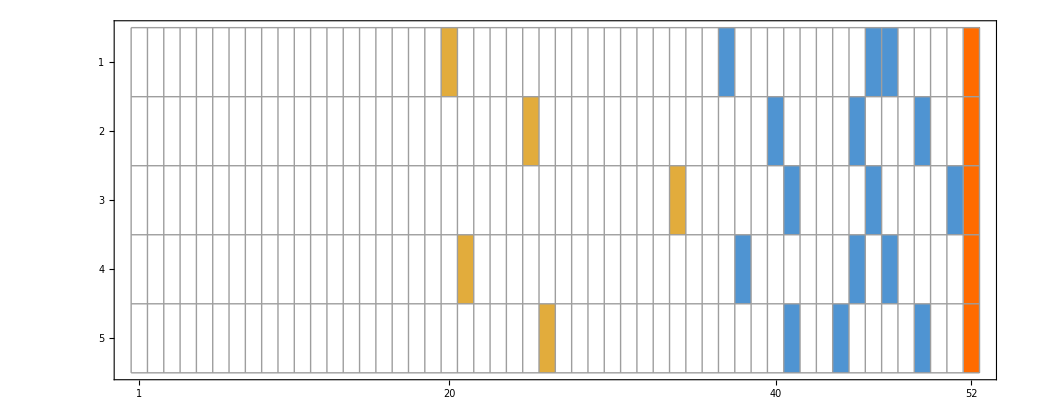

```mathematica
MatrixPlot[Table[BaseCoeff[k,"E"],{k,alfa1s}],Mesh->All]
```

```mathematica
TableForm[Table[If[k==l,{},Intersection[ListofVars[allGraphs5[k,"colofourrealnull"]],ListofVars[allGraphs5[l,"colofourrealnull"]]]],{k,alfa1s},{l,alfa1s}],TableHeadings->{Table[ShowGraph5Least[k],{k,alfa1s}],Table[ShowGraph5Least[k],{k,alfa1s}]}]
```

| -Graphics-361660 | -Graphics-317380 | -Graphics-296080 | -Graphics-361120 | -Graphics-317140
-Graphics-361660 |  | n12345 | n12345
n135x24 | n12345
n13x245 | n12345
-Graphics-317380 | n12345 |  | n12345 | n12345
n134x25 | n12345
n14x235
-Graphics-296080 | n12345
n135x24 | n12345 |  | n12345 | n12345
n124x35
-Graphics-361120 | n12345
n13x245 | n12345
n134x25 | n12345 |  | n12345
-Graphics-317140 | n12345 | n12345
n14x235 | n12345
n124x35 | n12345 |

```mathematica
(Map[Last[Last[First[Solve[#,n12345]]]]&,Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}]]//Total//Simplify)/.RepGraph["E"]
```

1/2 (-Graphics-575282+-Graphics-544922+-Graphics-454162+2 -Graphics-439081+-Graphics-189802+-Graphics-7282+2 -Graphics-49201+2 -Graphics-147481+2 -Graphics-133401+2 -Graphics-175681--Graphics-132842--Graphics-131762--Graphics-44282--Graphics-43802--Graphics-1682)

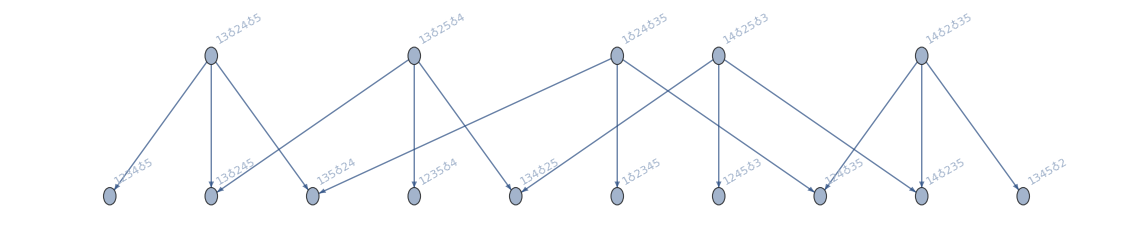

```mathematica
(Map[Last[Last[First[Solve[#,n12345]]]]&,Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}]]//Total//ListofVars//Sort//FormulaGraphReverse2)
```

```mathematica
(Eliminate[Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}],n13x24x5]//ExpressionToList)/.RepGraph["E"]//TableForm
```

2 -Graphics-590481==-Graphics-544922+-Graphics-133401+-Graphics-175681--Graphics-131762
-Graphics-175681==--Graphics-454162+-Graphics-439081+-Graphics-189802+-Graphics-44282--Graphics-43802
-Graphics-147481==-Graphics-544922--Graphics-439081--Graphics-7282+-Graphics-133401+-Graphics-175681--Graphics-131762+-Graphics-1682
-Graphics-133401==--Graphics-544922+-Graphics-454162+-Graphics-49201+-Graphics-131762--Graphics-44282

```mathematica
(Eliminate[Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}],n12345]//ExpressionToList)/.RepGraph["E"]//TableForm
```

-Graphics-575282==-Graphics-544922--Graphics-147481+-Graphics-175681+-Graphics-132842--Graphics-131762
-Graphics-175681==--Graphics-454162+-Graphics-439081+-Graphics-189802+-Graphics-44282--Graphics-43802
-Graphics-147481==-Graphics-544922--Graphics-439081--Graphics-7282+-Graphics-133401+-Graphics-175681--Graphics-131762+-Graphics-1682
-Graphics-133401==--Graphics-544922+-Graphics-454162+-Graphics-49201+-Graphics-131762--Graphics-44282

## Some reductions

```mathematica
system=Fold[And,Table[Simplify[allGraphs5[k,"colofourrealnull"]==0],{k,alfa1s}]]
```

2 n12345+n13x24x5==n1234x5+n135x24+n13x245&&2 n12345+n14x25x3==n1245x3+n134x25+n14x235&&2 n12345+n1x24x35==n124x35+n135x24+n1x2345&&2 n12345+n13x25x4==n1235x4+n134x25+n13x245&&2 n12345+n14x2x35==n124x35+n1345x2+n14x235

```mathematica
system2=Eliminate[system,n12345]
```

n1234x5==n1235x4+n134x25-n135x24+n13x24x5-n13x25x4&&n134x25==-n1245x3+n124x35+n1345x2+n14x25x3-n14x2x35&&n135x24==n1235x4-n124x35+n134x25+n13x245-n13x25x4-n1x2345+n1x24x35&&n13x245==-n1235x4+n1245x3+n13x25x4+n14x235-n14x25x3

```mathematica
system3=Eliminate[system2,n1235x4]
```

n1234x5==n124x35-n13x245+n13x24x5+n1x2345-n1x24x35&&n134x25==-n1245x3+n124x35+n1345x2+n14x25x3-n14x2x35&&n135x24==n1345x2+n14x235-n14x2x35-n1x2345+n1x24x35

```mathematica
system4=Eliminate[system3,n1245x3]
```

n124x35==n1234x5+n13x245-n13x24x5-n1x2345+n1x24x35&&n1345x2==n135x24-n14x235+n14x2x35+n1x2345-n1x24x35

```mathematica
system5=Eliminate[system4,n1x2345]
```

n124x35+n1345x2-n135x24-n13x245+n13x24x5+n14x235-n14x2x35==n1234x5

```mathematica
n124x35+n1345x2-n135x24-n13x245+n13x24x5+n14x235-n14x2x35==n1234x5/.RepGraph["E"]
```

-Graphics-439081+-Graphics-189802+-Graphics-49201--Graphics-147481--Graphics-133401+-Graphics-132842--Graphics-43802==-Graphics-575282

```mathematica
rep23={n1234x5->n124x35+n1345x2-n135x24-n13x245+n13x24x5+n14x235-n14x2x35}
```

{n1234x5→n124x35+n1345x2-n135x24-n13x245+n13x24x5+n14x235-n14x2x35}

```mathematica
Table[Simplify[allGraphs5[k,"colofourrealnull"]/.rep23]/.RepGraph["E"],{k,quads}]
```

{-6 -Graphics-590481+2 -Graphics-544922+-Graphics-529762+2 -Graphics-439081+4 -Graphics-189802+2 -Graphics-49201--Graphics-147481+-Graphics-175681--Graphics-529745--Graphics-175144+-Graphics-132842--Graphics-145864--Graphics-131762--Graphics-131244-2 -Graphics-43802+-Graphics-1312210,-6 -Graphics-590481+2 -Graphics-454162+3 -Graphics-439081+2 -Graphics-189802+-Graphics-21242+2 -Graphics-7282+2 -Graphics-49201--Graphics-133401--Graphics-439024--Graphics-6665+-Graphics-132842--Graphics-16204--Graphics-2184-2 -Graphics-43802--Graphics-1682+-Graphics-16210,-6 -Graphics-590481+2 -Graphics-544922+-Graphics-393922+2 -Graphics-439081+2 -Graphics-189802+2 -Graphics-7282+-Graphics-49201+-Graphics-147481--Graphics-393724--Graphics-145864--Graphics-5464--Graphics-265--Graphics-43802--Graphics-1682+-Graphics-610,-6 -Graphics-590481+2 -Graphics-454162+3 -Graphics-439081+4 -Graphics-189802+-Graphics-63202+4 -Graphics-49201-2 -Graphics-147481-2 -Graphics-133401+-Graphics-175681--Graphics-439024--Graphics-175144--Graphics-48604+2 -Graphics-132842--Graphics-58345--Graphics-44282-3 -Graphics-43802+-Graphics-437410,-6 -Graphics-590481+2 -Graphics-544922+2 -Graphics-454162+-Graphics-408962+2 -Graphics-7282+-Graphics-49201+-Graphics-133401+2 -Graphics-175681--Graphics-408785--Graphics-5464--Graphics-131762--Graphics-2184--Graphics-44282--Graphics-724+-Graphics-5410}

```mathematica
Table[Length[ListofVars[Simplify[allGraphs5[k,"colofourrealnull"]]]],{k,quads}]
```

{15,15,15,15,15}

```mathematica
Table[Length[ListofVars[Simplify[allGraphs5[k,"colofournull"]]]],{k,quads}]
```

{45,45,45,45,45}

```mathematica
Table[Length[ListofVars[Simplify[allGraphs5[k,"colotree"]]]],{k,quads}]
```

{5,5,5,5,5}

```mathematica
Table[allGraphs5[k,"colotree"]/.RepGraph["T"],{k,quads}]//TableForm
```

2 -Graphics-390141--Graphics-375481--Graphics-346201--Graphics-339160+-Graphics-331301
2 -Graphics-368980--Graphics-354340--Graphics-237701--Graphics-230721+-Graphics-222871
2 -Graphics-390141--Graphics-346201--Graphics-244141--Graphics-223180+-Graphics-199692
2 -Graphics-390141--Graphics-375481--Graphics-258682--Graphics-251680+-Graphics-243842
2 -Graphics-383080--Graphics-339160--Graphics-230721--Graphics-251680+-Graphics-207212

```mathematica
(Table[allGraphs5[k,"colotree"],{k,quads}]//Total//Simplify)/.RepGraph["T"]
```

6 -Graphics-390141+2 -Graphics-368980+2 -Graphics-383080-2 -Graphics-375481--Graphics-354340-2 -Graphics-346201-2 -Graphics-339160--Graphics-258682--Graphics-237701-2 -Graphics-230721-2 -Graphics-251680--Graphics-244141--Graphics-223180+-Graphics-331301+-Graphics-243842+-Graphics-222871+-Graphics-207212+-Graphics-199692

```mathematica
(Table[allGraphs5[k,"colotree"],{k,alfa1s}]//Total//Simplify)/.RepGraph["T"]
```

--Graphics-390141-2 -Graphics-368980-2 -Graphics-383080+-Graphics-354340+-Graphics-339160+-Graphics-251680+-Graphics-244141+-Graphics-223180

```mathematica
MatrixPlot[Table[BaseCoeff[k,"T"],{k,Join[quads,alfa1s,{lambdaKey,K5Key}]}],Mesh->All]
```

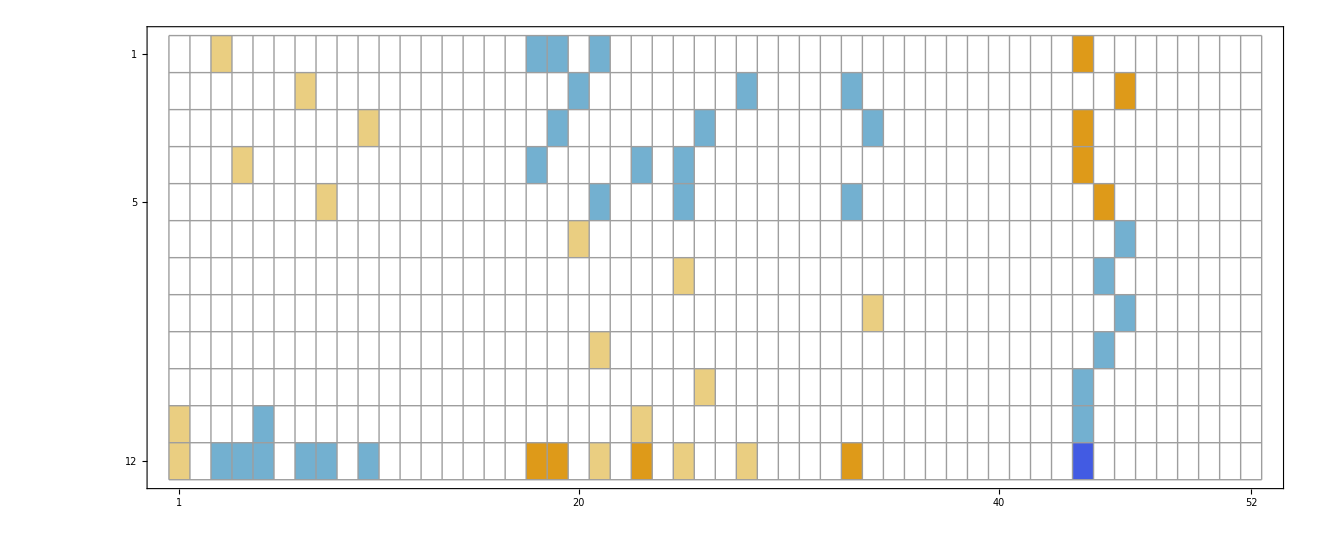

```mathematica
(Table[allGraphs5[k,"colotree"],{k,alfa1s}]//TableForm)/.RepGraph["T"]
```

--Graphics-368980+-Graphics-354340
--Graphics-383080+-Graphics-251680
--Graphics-368980+-Graphics-223180
--Graphics-383080+-Graphics-339160
--Graphics-390141+-Graphics-244141

```mathematica
allGraphs5[24414,"compwhy"]
```

The relation holds x24414== x31714(GreaterEqual) + 39014 (Greater)

```mathematica
ShowGraph5Least[39014]
```

-Graphics-390141

```mathematica
allGraphs5[39014,"compwhy"]
```

This is a planar contraction

```mathematica
Table[allGraphs5[k,"colotree"],{k,alfa1s}]//Total
```

-t1345x2-2 t134x25-2 t135x24+t13x24x5+t13x25x4+t14x25x3+t14x2x35+t1x24x35

```mathematica
-t1345x2-2 t134x25-2 t135x24+t13x24x5+t13x25x4+t14x25x3+t14x2x35+t1x24x35==0&&(Table[allGraphs5[k,"colotree"],{k,quads}]//Total)//Simplify
```

t13x24x5+t13x25x4+t14x25x3+t14x2x35+t1x24x35==t1345x2+2 (t134x25+t135x24)&&6 t1345x2+2 t134x25-2 t134x2x5+2 t135x24-2 t135x2x4-t13x24x5-2 t13x25x4+t13x2x4x5-t145x2x3-2 t14x25x3-t14x2x35+t14x2x3x5-t15x24x3-2 t1x245x3-t1x24x35+t1x24x3x5+t1x25x3x4+t1x2x35x4

```mathematica
Table[allGraphs5[k,"colotree"]/.RepGraph["T"],{k,alfa1s}]//TableForm
```

--Graphics-368980+-Graphics-354340
--Graphics-383080+-Graphics-251680
--Graphics-368980+-Graphics-223180
--Graphics-383080+-Graphics-339160
--Graphics-390141+-Graphics-244141

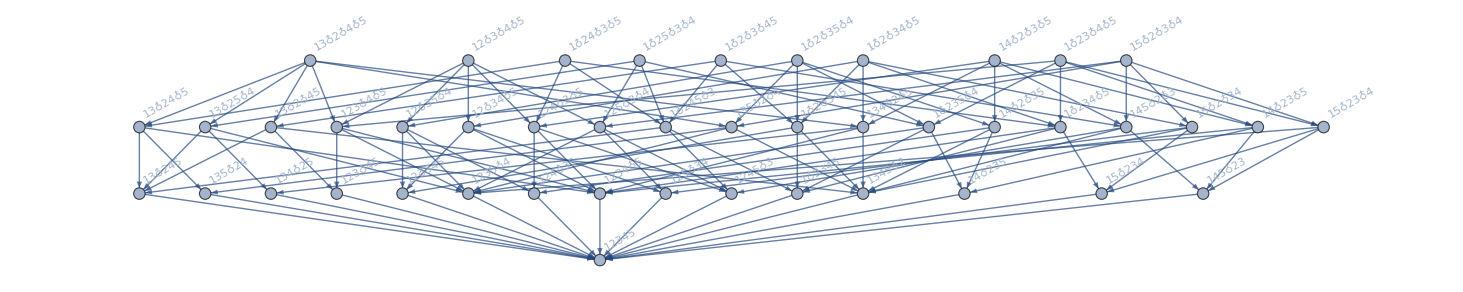

```mathematica
FormulaGraphReverse2[allGraphs5[quad1Key,"colofournull"]]
```

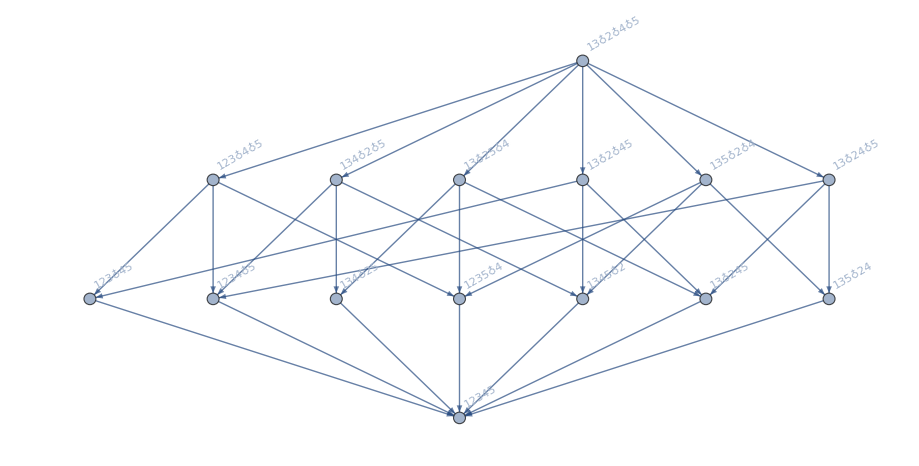

```mathematica
FormulaGraphReverse2[allGraphs5[quad1Key,"colofourrealnull"]]
```